Toolbar, Buttons, global vars and Misc. Functions

```mathematica
gameSettings=<| "roulType"-> "usRoul", "bankRoll"->10000, "minBet"->5, "maxBet"->1000, "initialBet"->5|>;
simulationSettings=<|"gamesPerTrial"-> 100, "numOfTrials"->100|>;
plotLiveUpdt = False;distEst=True;
```

```mathematica
{globRoulType, globBankRoll, globMinBet, globMaxBet, globInitBet} =Values[gameSettings];
{globGamesPerTrial, globNumOfTrials}=Values[simulationSettings];

barContents:=Module[{localRoulType, localBankRoll,localMinBet,localMaxBet,localInitBet,localGamesPerTrial, localNumOfTrials},
Column[{Row[{
"Roulette Type : ", PopupMenu[Dynamic[globRoulType],{"usRoul", "enRoul"}],
" Bank Roll: ",InputField[Dynamic[globBankRoll],FieldSize->4],
" Min Bet: ",InputField[Dynamic[globMinBet],FieldSize->4],
" Max.Bet: ",InputField[Dynamic[globMaxBet],FieldSize->4],
" Initial Bet: ",InputField[Dynamic[globInitBet],FieldSize->3]
}],
Row[{
"Games per Trial: ", InputField[Dynamic[globGamesPerTrial],FieldSize->5],
" Num of Trials: ", InputField[Dynamic[globNumOfTrials],FieldSize->5],"    ",
Checkbox[Dynamic[plotLiveUpdt]],"Live Plot (slow)  ",
Checkbox[Dynamic[distEst]],"Dist. estimate ",
Button["Update",(gameSettings=AssociationThread[Keys[gameSettings]-> {globRoulType, globBankRoll, globMinBet, globMaxBet, globInitBet}]; simulationSettings=AssociationThread[Keys[simulationSettings]-> {globGamesPerTrial, globNumOfTrials}];)]
}]
}]
]
```

```mathematica
SetOptions[EvaluationNotebook[],DockedCells->Cell[BoxData[ToBoxes[barContents]],
"DockedCell",Background->Lighter[RandomColor[], 0.75]]];
```

```mathematica
deletePrints[] :=Module[{},
NotebookFind[SelectedNotebook[], "Print", All, CellStyle];NotebookDelete[]]
deleteTempPrints[] :=Module[{},
NotebookFind[SelectedNotebook[],"PrintTemporary", All, CellStyle];NotebookDelete[]]
```

```mathematica
runBtnImg:=Image[Graphics[{Darker@Green,Disk[{0,0},0.6],Inset[Disk[{0,0},1]],
Inset[Style["Run",{White, Bold,30}]]},ImageSize->Tiny,Background->None]];
runBtn:=Button[runBtnImg,runSim[],Appearance->None, Method->"Queued"];
stopBtnImg:=Image[Graphics[{Red,Disk[{0,0},0.6],Inset[Disk[{0,0},1]],
Inset[Style["Stop",{White, Bold,30}]]},ImageSize->Tiny,Background->None]];
stopBtn:=Button[stopBtnImg,(endSim=1),Appearance->None];
clearImg:=Image[Graphics[{Gray,Disk[{0,0},0.6],Inset[Disk[{0,0},1]],
Inset[Style["Clear",{White, Bold,30}]]},ImageSize->Tiny,Background->None]];
clearBtn:=Button[clearImg,deletePrints[],Appearance->None];
```

```mathematica
{euRoul=Quiet@Import["http://www.onlinecasinoreporter.com/wp-content/uploads/2012/07/european-roulette-table.gif"],
usRoul=Quiet@Import["http://www.roulette-games.com/images/american_roulette_layout.gif"]};
```

Simulate roulette spin. Returns amount to multiply original bet by or -1 if the best is lost
TODO: parse number in string to number
TODO: Handle errors of incorrect inputs

```mathematica
simSpin[roulType_,betName_]:=Module[{denom=Switch[roulType,"enRoul",37,"usRoul",38,_,Abort[]],winOrLose,mult,oneToOneDist,twoToOneDist,straightUp},
oneToOneDist=BinomialDistribution[1,18/denom];(* Bet on Red, Black, Even, Odd*)
twoToOneDist=BinomialDistribution[1,12/denom];(* Bet on a column *) 
straightUp=BinomialDistribution[1,1/denom];(* Bet on single number *)

If[StringQ[betName],(* A few possibilities of bets...*)
If[StringMatchQ[betName,{"1to18","even","red","black","odd","19to36"},IgnoreCase->True], winOrLose=RandomVariate[oneToOneDist];mult=1;];
If[StringMatchQ[betName,{"1st12","2nd12","3rd12","2to1"},IgnoreCase->True], winOrLose=RandomVariate[twoToOneDist];mult=2;];
,(* Else, bet is single numbers 0 to 36*)
winOrLose=RandomVariate[straightUp]; mult=35;];
If[winOrLose==1,mult,-1]
]
```

Runs one trial with specified global parameters in: gameSettings and simulationSettings
- Choose betting style and strategy here

```mathematica
runTrial[]:=Module[{bankHistory={gameSettings["bankRoll"]},betAmount=gameSettings["minBet"],betType="black"},
Do[
(* simulate roulette spin with given bet and append result to bankHistory*)
bankHistory=Append[bankHistory, Last[bankHistory]+betAmount*simSpin[gameSettings["roulType"], betType]];

(* BETTING STRATEGY HERE .... changes bet amount of betType*)
(*If[Part[bankHistory,-1]-Part[bankHistory,-2]> 0,betAmount=gameSettings["minBet"], betAmount*=1];*) (* constant bet size*)
If[Part[bankHistory,-1]-Part[bankHistory,-2]> 0,betAmount=gameSettings["minBet"], betAmount*=2]; (* double after every loss*)

(* Game boundries:
 - Can't have negative bankroll- break instead
- Can't bet more than we have (bet all we have instead)
- Must stay within max/min betting limits       *)
If[(Last[bankHistory]≤ 0 ), Break[]];
If[betAmount> Last[bankHistory],betAmount=Last[bankHistory]];
betAmount=betAmount/.{x_/;x<gameSettings["minBet"]->gameSettings["minBet"],x_/;x>gameSettings["maxBet"]->gameSettings["maxBet"]};

,simulationSettings["gamesPerTrial"]-1];
bankHistory
]
```

Runs simulation with specified parameters and calculate metrics
TODO: Try decreasing Dynamic update rate for less frequent rendering
TODO: Look into interpolation for faster rendering
TODO: Look into Parallelize for faster rendering

Expected Value formula for multiple events:
E(X) 	= ∑X * P(X)
 E_blackOrRed = (18/38)(5) + (20/38)(-5) = -0.263158

#### runSim[]

```mathematica
runSim[]:=Module[{tScore95 = 1.96,cedF,dynPlot},
(* Global variables *)
trialHistory={};finalBankRoll={};gameHistory={};trialNum=0;endSim= 0;

PrintTemporary["Running simulation... ", Dynamic[trialNum], " of ", simulationSettings["numOfTrials"]];
PrintTemporary[ProgressIndicator[Dynamic[trialNum],{0,simulationSettings["numOfTrials"]}]];

(*------ Live update plot if checked off ------*)
If[plotLiveUpdt,
dynPlot=Dynamic[Style[ListLinePlot[trialHistory,
GridLines->Automatic,PlotRange->All,PlotLabel->"Simulation Results",
BaseStyle->{FontWeight->"Bold",FontSize->15},
Axes->True,Frame->True,FrameLabel->{"Bet Number","Bankroll ($)"},
ImageSize->Large,MaxPlotPoints->100,PerformanceGoal->"Speed"],Antialiasing->False]];
PrintTemporary[dynPlot];
];

(*------ Run simulation as long as the button is not pressed ------*)
Table[
If[endSim==1,Abort[],
singleGameHistory=runTrial[];
finalBankRoll=Append[finalBankRoll, Last[singleGameHistory]];(* snarf relevant data from trial for later analysis *)
trialHistory=Append[trialHistory, singleGameHistory];
trialNum++; 
];
,simulationSettings["numOfTrials"]
];
deleteTempPrints[];(* Delete prints once test is over*)

(*---------- 
Calculate some stats 
-----------*) 
If[distEst,
PrintTemporary["Calculating distribution..."];(* TODO: investigate other types of dist's*)
(*guessDist=Quiet[FindDistribution[finalBankRoll]];*)
guessDist = Quiet[SmoothKernelDistribution[finalBankRoll]];,
(*Else *)
guessDist = DataDistribution[0]; 
];

meanBankRoll=N[Mean[finalBankRoll]];
stdev=N[StandardDeviation[finalBankRoll]];
varian=N[Variance[finalBankRoll]];
(*----  Calculate Expected value: divide results into bins, find the probability of landing in each bin and multiply by the final bank amount. 
Sum them all up and divide by the number of simulations (trials) *)
resultBins=Gather[finalBankRoll];
expVal=N@Total[(First[#]-gameSettings["bankRoll"])*(Length[#]/simulationSettings["numOfTrials"])&/@resultBins]/simulationSettings["gamesPerTrial"];
(*--- TODO: Calculate the error of the expected value ---*)
stdevExpVal=N[StandardDeviation[(finalBankRoll-gameSettings["bankRoll"])/simulationSettings["gamesPerTrial"]]];
(*--- TODO: calculate confidence interval for any-type of distribution ---*)

(*Finalize results plot*) 
If[plotLiveUpdt,
finalPlot = dynPlot/.Dynamic->Evaluate;,
(*Else *)
finalPlot= ListLinePlot[trialHistory,
GridLines->Automatic,PlotRange->All,PlotLabel->"Simulation Results",
BaseStyle->{FontWeight->"Bold",FontSize->15},
Axes->True,Frame->True,FrameLabel->{"Bet Number","Bankroll ($)"},
ImageSize->Large,MaxPlotPoints->100,PerformanceGoal->"Speed"];
];

(*---------- 
Print results 
-----------*) 
Print[Style["Summary:",Bold,16]];
Print[Row[{finalPlot,
Column[{
Grid[{
{"Games per trial: ", simulationSettings["gamesPerTrial"]},
{"Number of trials: ", simulationSettings["numOfTrials"]},
{"Average final bankroll: ",meanBankRoll},
{"Average earnings: ", ( meanBankRoll-gameSettings["bankRoll"])},
{"Expected value: ",ToString[expVal]}
},Frame->All,Background->{{LightGray}}],

Show[
cedF[{{xmin_,xmax_},{ymin_,ymax_}},___]:=
{If[xmax≤gameSettings["bankRoll"],LightRed,Sequence[]],
If[xmax>gameSettings["bankRoll"],LightGreen,Sequence[]],
Rectangle[{xmin,ymin},{xmax,ymax}]};

Histogram[finalBankRoll,100,"PDF",ChartStyle->"Pastel",ChartElementFunction->cedF,Epilog->{Directive[{Blue,Thin,Dashed}],
Line[{{meanBankRoll,0},{meanBankRoll,600}}]
}]
,
Plot[PDF[guessDist,x],{x,Min[finalBankRoll],Max[finalBankRoll]}]
,
ImageSize->Medium,PlotLabel-> "Final Bankroll",PlotRange->{{Min[finalBankRoll],Max[finalBankRoll]},All}]
}](*End of Column *)
}]];
]
```

{-Graphics-,-Graphics-,-Graphics-}

Summary:

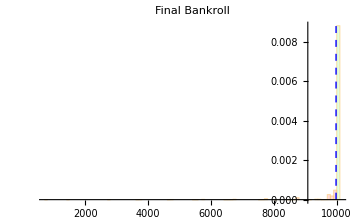
-Graphics-Games per trial:  | 20
Number of trials:  | 50000
Average final bankroll:  | 9978.86
Average earnings:  | -21.1422
Expected value:  | -1.05711
-Graphics-

Summary:

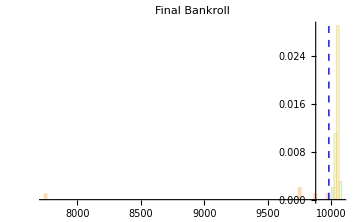
-Graphics-Games per trial:  | 20
Number of trials:  | 50
Average final bankroll:  | 9979.7
Average earnings:  | -20.3
Expected value:  | -1.015
-Graphics-

```mathematica
{runBtn,stopBtn,clearBtn}
```

## Making code cloud-deployable

#### runSimFunc[inputs_]

```mathematica
runSimFunc[roulType_, bankRoll_, minBet_,maxBet_, initBet_, gamePerTrial_, trials_]:=Module[{trialHistory={}, finalBankRoll={}, gameHistory={}, trialNum=0,dynPlot,plotLiveUpdt=False},

(* Updates values from function into global settings *)
(gameSettings=AssociationThread[Keys[gameSettings]-> {roulType, bankRoll, minBet, maxBet, initBet}]; simulationSettings=AssociationThread[Keys[simulationSettings]-> {gamePerTrial, trials}];);

(* Run trials without Prints *)
Table[
singleGameHistory=runTrial[];

(* snarf relevant data from trial for later analysis *)
finalBankRoll=Append[finalBankRoll, Last[singleGameHistory]];
trialHistory=Append[trialHistory, singleGameHistory];
,simulationSettings["numOfTrials"]
];

(*-------- Calculate some stats *) 
meanBankRoll=N[Mean[finalBankRoll]];
stdev=N[StandardDeviation[finalBankRoll]];
varian=N[Variance[finalBankRoll]];
(*resultCI = MeanCI[finalBankRoll-gameSettings["bankRoll"], ConfidenceLevel->.95]/simulationSettings["gamesPerTrial"];*)
expVal=Round[Mean[finalBankRoll-gameSettings["bankRoll"]]/simulationSettings["gamesPerTrial"],0.0001];
stdevExpVal=N[StandardDeviation[(finalBankRoll-gameSettings["bankRoll"])/simulationSettings["gamesPerTrial"]]];

finalPlot= ListLinePlot[trialHistory,
GridLines->Automatic,PlotRange->All,PlotLabel->"Simulation Results",
BaseStyle->{FontWeight->"Bold",FontSize->15},
Axes->True,Frame->True,FrameLabel->{"Bet Number","Bankroll ($)"},
ImageSize->Large,MaxPlotPoints->100,PerformanceGoal->"Speed"];

guessDist=FindDistribution[finalBankRoll];

Row[{finalPlot,
Column[{
Grid[{
{"Games per trial: ", simulationSettings["gamesPerTrial"]},
{"Number of trials: ", simulationSettings["numOfTrials"]},
(*{"% of bankrupcies: ", N[Count[finalBankRoll,0]/simulationSettings["numOfTrials"]]*100},*)
{"Average earnings: ",  N[Mean[finalBankRoll]-gameSettings["bankRoll"]]},
{"Average final bankroll: ", N[Mean[finalBankRoll]]}
(*{"Expected value : ",ToString[expVal]<>" ± "<>ToString[Round[( Differences[resultCI][[1]]/2),0.0001]]},*)
(*{"resultCI: ", ToString[resultCI]}*)
(*{"95% CI of E(x) +-: ", (1.96*stdevExpVal)}*)

},Frame->All,Background->{{LightGray}}]
,
Show[Histogram[finalBankRoll,100,"PDF"],
Plot[PDF[NormalDistribution[meanBankRoll,stdev],x],{x,meanBankRoll-3stdev,meanBankRoll+3stdev}],ImageSize->Medium,PlotLabel-> "Final Bankroll",PlotRange-> All]
}]

}]
]
```

### FormFunction for CloudDeploy[]

```mathematica
myCloudForm=FormFunction[{
"RouletteType"-> {"usRoul", "enRoul"}, "Bankroll"-> <|"Interpreter"->"Number","Input"->10000|>, "MinBet"->  <|"Interpreter"->"Number","Input"->5|>, "MaxBet"->  <|"Interpreter"->"Number","Input"->1000|>, "InitialBet" ->  <|"Interpreter"->"Number","Input"->5|>,
"GamesPerTrial"->  <|"Interpreter"->"Number","Input"->100|>,
"TrialsPerSimulation"->  <|"Interpreter"->"Number","Input"->100|>}, 

runSimFunc[#RouletteType, #Bankroll, #MinBet, #MaxBet, #InitialBet, #GamesPerTrial, #TrialsPerSimulation]&, 

FormLayoutFunction->Function[Column[{
Row[{#["RouletteType"]," ", #["Bankroll"] }],
Row[{#["MinBet"]," ",#["MaxBet"]," ",#["InitialBet"]}],
Row[{#["GamesPerTrial"]," ",#["TrialsPerSimulation"]}] 
}]
],
AppearanceRules-><|"Title"->"Game Info: " , "SubmitLabel"-> "Simulate"|>]
```

FormFunction[]

```mathematica
CloudDeploy[myCloudForm]
```

CloudObject[https://www.wolframcloud.com/objects/bb1d05f3-a979-4058-9c84-2e9144be85c9]

#### --- Testing package functionality in cloud deploy

```mathematica
CloudDeploy[MeanCI[{-155,-65,-55,-65,-35,-25,-5,-25,55,15,15,-35,-95,-115,-45,-75,-55,-75,5,-65,5,-5,35,-85,-45,25,5,-55,25,-15,-95,65,15,-15,-15,-25,-65,-65,5,45,-115,65,-105,25,-45,-45,-55,25,25,-35,-15,-5,-5,-35,-15,35,45,-95,-5,5,15,15,-45,65,-5,-15,-85,-85,-125,-15,65,-75,-5,-35,-75,5,85,-35,-95,-5,45,15,-135,-25,-45,65,-5,15,-15,-75,65,-85,-35,-5,-75,-25,55,-15,25,-65},ConfidenceLevel->0.95]]
```

CloudObject[https://www.wolframcloud.com/objects/09f44780-958c-4b1a-93fe-114dd2d9accc]

### Delete cloud objects...

```mathematica
cloudObjs=CloudObjects[".Objects"]
```

{}

```mathematica
DeleteObject/@cloudObjs
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}